```mathematica
Clear[m,c,t,T,P,T0,σ,A,ϵ]
```

```mathematica
Solve[(m*c)/t(T-T0)+A*σ*ϵ(T^4-T0^4)==P,T];
```

```mathematica
T0=21+273.15;P=4;σ=5.67*10^-8;m=7.656;c=0.456;A=0.00129;
```

```mathematica
Tfinal[t_,ϵ_]:=-1/2 √((4 2^(1/3) (P t+c m T0+A t T0^4 ϵ σ))/((-27 A c^2 m^2 t ϵ σ+√(729 A^2 c^4 m^4 t^2 ϵ^2 σ^2+6912 A^3 t^3 ϵ^3 σ^3 (P t+c m T0+A t T0^4 ϵ σ)^3))^(1/3))-((-27 A c^2 m^2 t ϵ σ+√(729 A^2 c^4 m^4 t^2 ϵ^2 σ^2+6912 A^3 t^3 ϵ^3 σ^3 (P t+c m T0+A t T0^4 ϵ σ)^3))^(1/3))/(3 2^(1/3) A t ϵ σ))+1/2 √(-(4 2^(1/3) (P t+c m T0+A t T0^4 ϵ σ))/((-27 A c^2 m^2 t ϵ σ+√(729 A^2 c^4 m^4 t^2 ϵ^2 σ^2+6912 A^3 t^3 ϵ^3 σ^3 (P t+c m T0+A t T0^4 ϵ σ)^3))^(1/3))+((-27 A c^2 m^2 t ϵ σ+√(729 A^2 c^4 m^4 t^2 ϵ^2 σ^2+6912 A^3 t^3 ϵ^3 σ^3 (P t+c m T0+A t T0^4 ϵ σ)^3))^(1/3))/(3 2^(1/3) A t ϵ σ)+(2 c m)/(A t ϵ σ √((4 2^(1/3) (P t+c m T0+A t T0^4 ϵ σ))/((-27 A c^2 m^2 t ϵ σ+√(729 A^2 c^4 m^4 t^2 ϵ^2 σ^2+6912 A^3 t^3 ϵ^3 σ^3 (P t+c m T0+A t T0^4 ϵ σ)^3))^(1/3))-((-27 A c^2 m^2 t ϵ σ+√(729 A^2 c^4 m^4 t^2 ϵ^2 σ^2+6912 A^3 t^3 ϵ^3 σ^3 (P t+c m T0+A t T0^4 ϵ σ)^3))^(1/3))/(3 2^(1/3) A t ϵ σ))))-273.15;
```

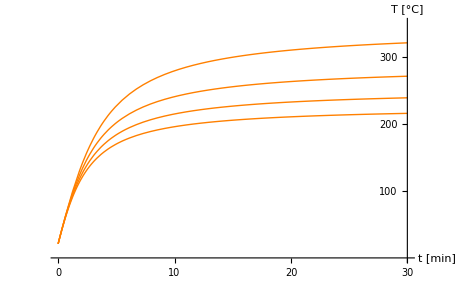

```mathematica
Plot[{Tfinal[t,1],Tfinal[t,.8],Tfinal[t,.6],Tfinal[t,.4]},{t,0,1800}, AxesLabel->{"t [min]","T [°C]"} ,PlotRange->{0,350},PlotStyle->{Orange}, Ticks->{{{0,0},{600,10},{1200,20},{1800,30}},{100,200,300}},AxesOrigin->{1800,0}]
```

```mathematica
tfinal[3000.0]
```

532.164

Equations for Power:

P = A σ ϵ (T^4-T_o^4) 

Q = m c (T-T_o)

P = dQ/dt= (m c (T-T_0))/dt

ϵ =  (P_in-(m c (T-T_0))/dt)/(A σ  (T^4-T_o^4))
ϵ =  P_in/(A σ  (T^4-T_o^4))
ϵ =  (-m c (T-T_0))/(A σ dt  (T^4-T_o^4))